```mathematica
Module[{a=158.4,b=0.288,c,d,e},NonlinearModelFit[data,Re[{c/(1+Exp[d-Log[a/(b* x)-1/b]/e])}],{{d,2.6},{c,160},{e,0.45}},x]]
```

NonlinearModelFit::fitd: First argument data in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[data,{Re[c$1660/(1+ⅇ^(d$1660-Log[-3.47222+550./x]/e$1660))]},{{d$1660,2.6},{c$1660,160},{e$1660,0.45}},x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.86541 | 0.00671328 | 724.745 | 9.49225×10^-14
x | 0.674422 | 0.12464 | 5.41096 | 0.0029163

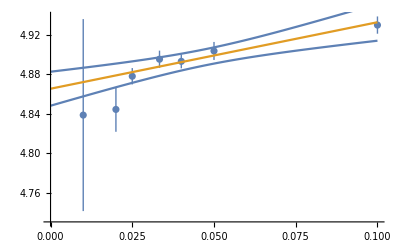

```mathematica
data={{{1/10,4.92997},ErrorBar[0.00875039]},{{1/20,4.90374},ErrorBar[0.00912412]},{{1/25,4.89318},ErrorBar[0.00707122]},{{1/30,4.89534},ErrorBar[0.00870608]},{{1/40,4.87807},ErrorBar[0.00829155]},{{1/50,4.84442},ErrorBar[0.0226886]},{{1/100,4.83867},ErrorBar[0.0973819]}};
error=data[[All,2]]/.ErrorBar[x_]->x;
t=Table[{data[[i,1,1]],Around[data[[i,1,2]],error[[i]]]},{i,Length[error]}];
lmf=LinearModelFit[data[[All,1]],x,x,Weights->1/error^2];
lmf["ParameterTable"]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,0.1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/yinsh/Chi8/data/freezeout/fitSTAR

```mathematica
data=Import["stardata.dat"][[All,{2,4,5}]]
```

{{399.8,143.8,2.7},{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5},{69.2,164.3,3.6},{27.,167.8,4.2}}

{2.7,3.2,3.1,3.,3.5,3.6,4.2}

| Estimate | Standard Error | t-Statistic | P-Value
c | 162.217 | 1.55268 | 104.476 | 1.52334×10^-9
e | 0.453047 | 0.0164501 | 27.5407 | 1.18117×10^-6

162.217/(1+13.4637/(-3.47222+4539.93/x)^2.20728)

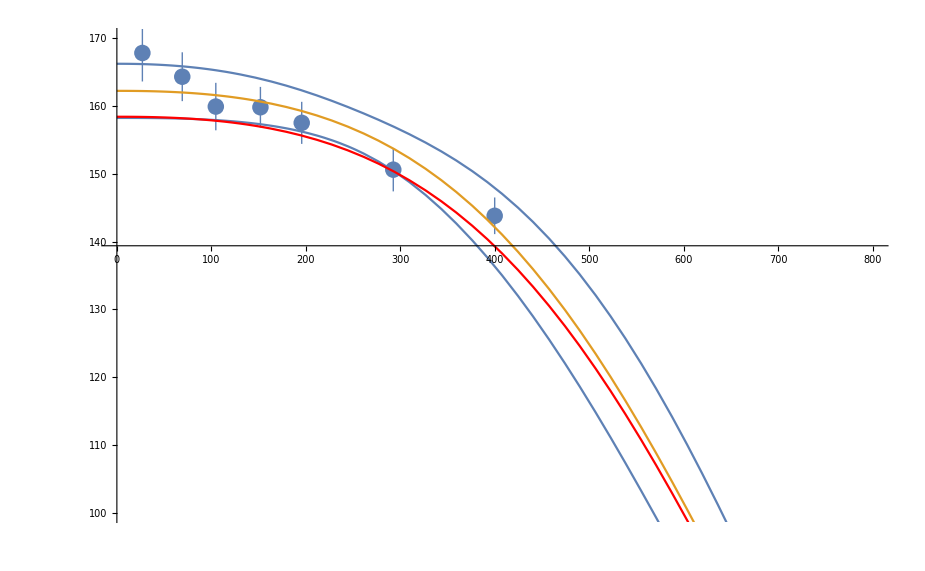

```mathematica
(*data={{{1/10,4.92997},ErrorBar[0.00875039]},{{1/20,4.90374},ErrorBar[0.00912412]},{{1/25,4.89318},ErrorBar[0.00707122]},{{1/30,4.89534},ErrorBar[0.00870608]},{{1/40,4.87807},ErrorBar[0.00829155]},{{1/50,4.84442},ErrorBar[0.0226886]},{{1/100,4.83867},ErrorBar[0.0973819]}};*)
error=data[[All,-1]]
t=Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}];
lmf=NonlinearModelFit[data[[All,{1,2}]],c/(1+Exp[2.6-Log[1307.5/(0.288* x)-1/0.288]/e]),{{c,160},{e,1/2}},x,Weights->1/error^2];
lmf["ParameterTable"]
lmf[x]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red],PlotRange->{{0,800},{100,170}}]
```

```mathematica
lmf["MeanPredictionBands"]
```

{162.217/(1+13.4637/(-3.47222+4539.93/x)^2.20728)-2.57058 √(1/((13.4637+(-3.47222+4539.93/x)^2.20728)^4)(437.012 (-3.47222+4539.93/x)^4.41455+64.9168 (-3.47222+4539.93/x)^6.62183+2.4108 (-3.47222+4539.93/x)^8.82911+(-4865.55 (-3.47222+4539.93/x)^4.41455-361.382 (-3.47222+4539.93/x)^6.62183) Log[-3.47222+4539.93/x]+30640. (-3.47222+4539.93/x)^4.41455 Log[-3.47222+4539.93/x]^2)),162.217/(1+13.4637/(-3.47222+4539.93/x)^2.20728)+2.57058 √(1/((13.4637+(-3.47222+4539.93/x)^2.20728)^4)(437.012 (-3.47222+4539.93/x)^4.41455+64.9168 (-3.47222+4539.93/x)^6.62183+2.4108 (-3.47222+4539.93/x)^8.82911+(-4865.55 (-3.47222+4539.93/x)^4.41455-361.382 (-3.47222+4539.93/x)^6.62183) Log[-3.47222+4539.93/x]+30640. (-3.47222+4539.93/x)^4.41455 Log[-3.47222+4539.93/x]^2))}

```mathematica
export={lmf["MeanPredictionBands"],lmf[x]}/.x->{22.3123,68.9203,78.4475,106.892,148.986,196.77,252.608,303.224,406.359}
```

{{{158.221,158.125,158.083,157.888,157.349,156.174,153.543,149.421,135.24},{166.177,165.833,165.708,165.208,164.087,162.237,159.38,156.256,147.186}},{162.199,161.979,161.895,161.548,160.718,159.206,156.461,152.838,141.213}}

```mathematica
exp7=Transpose[{{158.22131413171184,158.12543008868985,158.08272958026592,157.88823578063685,157.3488875625452,156.1743113574977,153.54260856723175,149.42096014040877,135.23995860136924},{166.17661492225972,165.8333694752669,165.7082060234118,165.20772158533637,164.0873523363664,162.2373987283354,159.37997420465115,156.25580406364318,147.18556703491257},{162.19896452698578,161.97939978197837,161.89546780183886,161.5479786829866,160.7181199494558,159.20585504291654,156.46129138594145,152.83838210202597,141.2127628181409}}]
```

{{158.221,166.177,162.199},{158.125,165.833,161.979},{158.083,165.708,161.895},{157.888,165.208,161.548},{157.349,164.087,160.718},{156.174,162.237,159.206},{153.543,159.38,156.461},{149.421,156.256,152.838},{135.24,147.186,141.213}}

```mathematica
mub=Table[i*5,{i,1,160}];
```

```mathematica
exp7data={lmf[x]}/.x->mub
```

{{162.217,162.214,162.21,162.203,162.194,162.182,162.167,162.149,162.128,162.104,162.076,162.045,162.01,161.971,161.928,161.88,161.829,161.773,161.712,161.646,161.576,161.5,161.42,161.333,161.241,161.144,161.04,160.931,160.815,160.693,160.564,160.428,160.286,160.136,159.979,159.815,159.643,159.463,159.274,159.078,158.873,158.66,158.437,158.206,157.966,157.716,157.456,157.186,156.907,156.617,156.316,156.005,155.683,155.35,155.006,154.649,154.282,153.902,153.51,153.106,152.689,152.259,151.816,151.361,150.891,150.408,149.912,149.401,148.876,148.337,147.783,147.214,146.631,146.032,145.418,144.789,144.145,143.484,142.808,142.116,141.408,140.684,139.943,139.187,138.413,137.624,136.817,135.995,135.155,134.299,133.427,132.537,131.631,130.709,129.77,128.815,127.843,126.855,125.85,124.83,123.794,122.742,121.675,120.592,119.494,118.381,117.253,116.112,114.956,113.786,112.602,111.406,110.197,108.975,107.741,106.496,105.239,103.972,102.694,101.407,100.11,98.8044,97.4904,96.1685,94.8394,93.5036,92.1615,90.8139,89.4613,88.1042,86.7432,85.3791,84.0123,82.6435,81.2733,79.9023,78.5312,77.1605,75.791,74.4231,73.0576,71.695,70.336,68.9812,67.6312,66.2865,64.9478,63.6157,62.2907,60.9733,59.6642,58.3638,57.0728,55.7915,54.5205,53.2604,52.0114,50.7742,49.5492,48.3367}}

```mathematica
Export["sevenpointfitphase.dat",exp7data]
```

sevenpointfitphase.dat

```mathematica
Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}]
```

{{399.8,143.82.7},{292.5,150.63.2},{195.6,157.53.1},{151.9,159.83.0},{104.7,159.93.5},{69.2,164.4.},{27.,168.4.}}

```mathematica
error=data[[All,-1]]
```

{2.7,3.2,3.1,3.,3.5,3.6,4.2}

```mathematica
{lmf["MeanPredictionBands"],lmf[x]}/.x->100
```

{{157.946,165.347},161.646}

```mathematica
data={{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5}}
```

{{292.5,150.6,3.2},{195.6,157.5,3.1},{151.9,159.8,3.},{104.7,159.9,3.5}}

{3.2,3.1,3.,3.5}

| Estimate | Standard Error | t-Statistic | P-Value
c | 161.439 | 0.507481 | 318.119 | 9.88131×10^-6
e | 0.474767 | 0.00776693 | 61.1267 | 0.000267525

161.439/(1+13.4637/(-3.47222+4539.93/x)^2.1063)

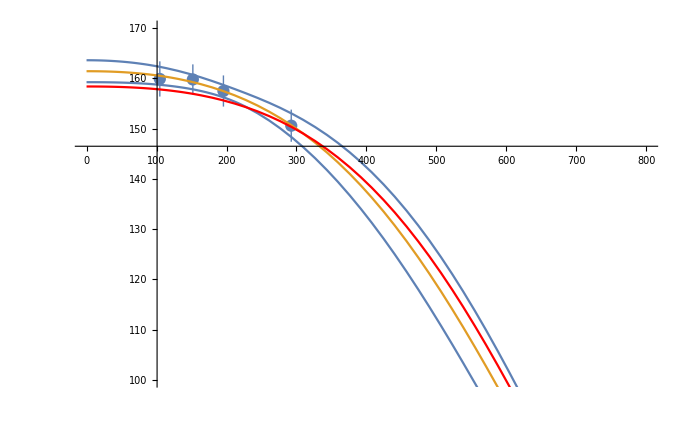

```mathematica
error=data[[All,-1]]
t=Table[{data[[i,1]],Around[data[[i,2]],error[[i]]]},{i,Length[error]}];
lmf=NonlinearModelFit[data[[All,{1,2}]],c/(1+Exp[2.6-Log[1307.5/(0.288* x)-1/0.288]/e]),{{c,160},{e,1/2}},x,Weights->1/error^2];
lmf["ParameterTable"]
lmf[x]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red],PlotRange->{{0,800},{100,170}}]
```

```mathematica
export={lmf["MeanPredictionBands"],lmf[x]}/.x->{22.3123,68.9203,78.4475,106.892,148.986,196.77,252.608,303.224,406.359}
```

{{{159.245,159.077,159.008,158.705,157.908,156.189,152.382,147.111,131.499},{163.572,163.084,162.913,162.249,160.824,158.648,155.652,152.259,141.482}},{161.408,161.08,160.961,160.477,159.366,157.418,154.017,149.685,136.49}}

```mathematica
exp4=Transpose[{{159.2451405725481,159.07695501798005,159.00758761997403,158.7051389360926,157.9077370306953,156.18867704217698,152.38220395585265,147.11058393969924,131.4986919237775},{163.571758650295,163.08394426432952,162.91348743423922,162.24896859974936,160.82423168700186,158.64794794776444,155.65171560134903,152.25943571025854,141.48195097574987},{161.40844961142156,161.0804496411548,160.96053752710662,160.47705376792098,159.36598435884858,157.4183124949707,154.01695977860084,149.6850098249789,136.49032144976368}}]
```

{{159.245,163.572,161.408},{159.077,163.084,161.08},{159.008,162.913,160.961},{158.705,162.249,160.477},{157.908,160.824,159.366},{156.189,158.648,157.418},{152.382,155.652,154.017},{147.111,152.259,149.685},{131.499,141.482,136.49}}

```mathematica
Export["fourpointfitphase.dat",exp4data]
```

fourpointfitphase.dat

```mathematica
exp4data={lmf[x]}/.x->mub
```

{{161.438,161.434,161.426,161.415,161.4,161.381,161.358,161.331,161.299,161.262,161.221,161.175,161.124,161.068,161.006,160.939,160.866,160.788,160.703,160.612,160.515,160.412,160.302,160.185,160.061,159.931,159.792,159.647,159.494,159.333,159.164,158.987,158.801,158.608,158.405,158.194,157.974,157.744,157.505,157.257,156.999,156.73,156.452,156.164,155.865,155.555,155.235,154.903,154.56,154.206,153.841,153.463,153.074,152.672,152.259,151.832,151.394,150.942,150.478,150.,149.509,149.005,148.487,147.955,147.41,146.85,146.277,145.689,145.087,144.47,143.839,143.193,142.532,141.857,141.166,140.46,139.74,139.004,138.253,137.487,136.705,135.909,135.097,134.27,133.427,132.57,131.697,130.809,129.906,128.988,128.056,127.108,126.146,125.17,124.179,123.174,122.155,121.122,120.075,119.015,117.942,116.856,115.757,114.646,113.522,112.387,111.24,110.082,108.913,107.734,106.544,105.345,104.136,102.919,101.692,100.458,99.2157,97.9663,96.7101,95.4475,94.179,92.9051,91.6263,90.3431,89.0559,87.7653,86.4718,85.1759,83.8781,82.5789,81.2789,79.9785,78.6783,77.3789,76.0807,74.7842,73.49,72.1987,70.9106,69.6263,68.3463,67.0712,65.8013,64.5372,63.2794,62.0283,60.7844,59.5481,58.3199,57.1001,55.8893,54.6878,53.496,52.3143,51.1431,49.9827,48.8335,47.6958,46.5699,45.4561}}